```mathematica
GAUSS[time_,delay_,sigma_]:=1./(sigma*Sqrt[2.*Pi])Exp[-0.5*((time-delay)/sigma)^2]
```

```mathematica
t0=380.;
J0=0.2;
EE = 0.0364;
BETA =100.0;
MU=0.4;
tc=0.658;
500/tc
FWHMp =100;(*fs*)
sigmafsp =FWHMp/2.355; (*fs*)
sigmap = sigmafsp/tc (*1/eV*)
t00 = 250/tc
```

759.878

64.5332

379.939

```mathematica
omega =0.207
```

0.207

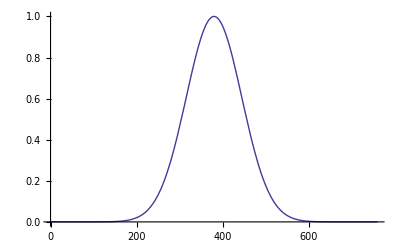

```mathematica
Plot[{(sigmap*Sqrt[2.*Pi])GAUSS[t,t0 ,sigmap]},{t,0,500/tc}]
```

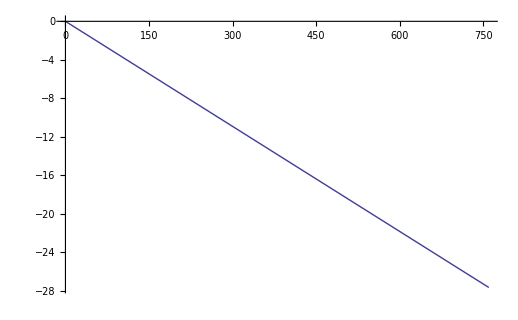

```mathematica
Plot[{-EE*t},{t,0,500/tc}]
```

```mathematica
({10, 20, 40, 60 ,80, 100}/2.355)/tc
```

{6.45332,12.9066,25.8133,38.7199,51.6266,64.5332}

```mathematica
f[w_,beta_]:=1./(Exp[w*beta]+1.)
epsilon[k_,J0_,EE_,t1_,t2_]:=-2.*J0*Cos[k-0.5*EE*(t1+t2)]
```

```mathematica
Photo[Omega_,k_,sigma_]:=Im[NIntegrate[GAUSS[t1,t0,sigma]*GAUSS[t2,t0,sigma]*I*f[epsilon[k,J0,EE,t1,t2]-MU,BETA]*Exp[I*(Omega+MU)*(t1-t2)-2.*I*epsilon[k,J0,EE,0.,0.]/EE*Sin[EE*(t1-t2)/2.]],{t1,0.,500./tc},{t2,0.,500./tc},Method->{"RiemannRule","Type"->"Right","Points"->100},MaxRecursion->0]]
```

```mathematica
Photo[0.0,Pi,15]
```

0.866082

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
ListLinePlot[{Photo[Range[-0.9,-0.5,0.01],0.0,6.45],Photo[Range[-0.9,-0.5,0.01],0.0,12.9],Photo[Range[-0.9,-0.5,0.01],0.0,25.81],Photo[Range[-0.9,-0.5,0.01],0.0,38.71],Photo[Range[-0.9,-0.5,0.01],0.0,51.62],Photo[Range[-0.9,-0.5,0.01],0.0,64.53]},PlotRange->All,Frame->True,PlotStyle->{Thickness[0.005]},FrameLabel->{"FREQUENCY","IPHOTO"},PlotLegend->{"FWHM=10 fs","FWHM=20 fs","FWHM=40 fs","FWHM=60 fs","FWHM=80 fs","FWHM=100 fs",15},LegendPosition->{-0.7,0.1},LegendShadow->None]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t1 near {t1, t2} = {759.878, 759.878}. NIntegrate obtained -3.55694×10^-17 + 0.639085\ ⅈ and 0.0000202462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t2 near {t1, t2} = {759.878, 759.878}. NIntegrate obtained 1.1728×10^-17 + 0.692141\ ⅈ and 0.000014879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t2 near {t1, t2} = {759.878, 759.878}. NIntegrate obtained 1.46509×10^-17 + 0.743887\ ⅈ and 0.0000108387 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

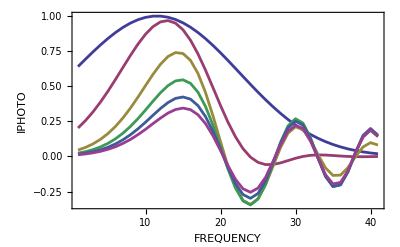

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t2 near {t1, t2} = {500., 500.}. NIntegrate obtained 1.98206×10^-19 + 0.0118418\ ⅈ and 3.7714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t1 near {t1, t2} = {500., 500.}. NIntegrate obtained -1.82705×10^-18 + 0.0174131\ ⅈ and 4.2904×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t2 near {t1, t2} = {500., 500.}. NIntegrate obtained 1.61868×10^-18 + 0.0252107\ ⅈ and 4.96318×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

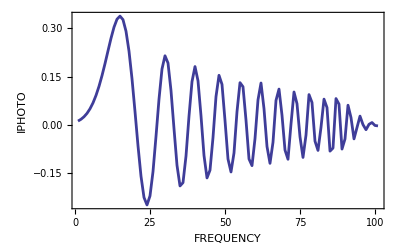

```mathematica
ListLinePlot[{Photo[Range[-0.9,+0.1,0.01],0.0,65]},PlotRange->All,Frame->True,PlotStyle->{Thickness[0.005]},FrameLabel->{"FREQUENCY","IPHOTO"},PlotLegend->{"σ=20", "σ=30","σ=40","σ=50"},LegendPosition->{-0.5,0.5},LegendShadow->None]
```